## Test functions

```mathematica
H1=0.5;
H2=0.5;
L=10;
```

```mathematica
U[x_, y_,t_]:=Erf[-(x-t)/√2]+(x-t)y^2/2Exp[-(x-t)^2/2]+1;
W[x_, y_,t_]:=y Exp[-(x-t)^2/2];
Manipulate[Plot[U[x,0,t],{x,0,L},PlotRange->Full],{t,0,10}]
```

Plot::plln: Limiting value L in {x,0,L} is not a machine-sized real number.

```mathematica
pad=1;
scale=0.5;
opts=Sequence[BoundaryStyle->Black,Frame->False,Axes->False,PlotRange->{{-L,2L},{-H1-H2-pad,H1+H2+pad}},PerformanceGoal->"Quality"];
plot[t_]:=Show[ParametricPlot[{x+scale U[x,y,t],y+scale W[x,y,t]},{x,-pad,L+pad},{y,-H1-H2,H1+H2},Mesh->{23,7},PlotStyle->Gray,Evaluate@opts],
ParametricPlot[{x+scale U[x,y,t],y+scale W[x,y,t]},{x,-pad,L+pad},{y,-H1,H1},Mesh->{23,3},PlotStyle->Gray,Evaluate@opts]];
Animate[plot[t],{t,-3pad,L+3pad}]
```

```mathematica
table=Monitor[Table[plot[t],{t,-3pad,L+3pad,0.1}],t];
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["wave.gif",table]
```

wave.gif

## Soliton in layered plate

```mathematica
l=10^10;
m=10^10;
n=10^10;
ν=0.33;
H1=0.8;
H2=0.8;
L=10;
A=0.01;
Em=5*10^9;
ρ=1060;
β2=(2(1-2ν)(1+ν))/(3Em(1-ν)^2)((l+2m)(1-2ν)^2+6ν(1-ν)m);
β=3 Em/(1-ν^2)+2l(1-2ν)^3/(1-ν)^3+4m(1-2ν)(1-ν+ν^2)/(1-ν)^3;
Simplify[3/2(1+β2)-β/(2Em)(1-ν^2)];
c=Sqrt[Em/ρ];
v=Sqrt[(A β)/(3ρ)+c^2/(1-ν^2)];
λ=Sqrt[(ν^2 (H1+H2)^2)/(1-ν)^2(1/3+Em/(2(1-ν)A β))];
U[x_,y_,t_]=-A (Integrate[ Cosh[(x-v t)/λ]^-2,x]-0.5+ν/(2(1-ν))y^2 D[Cosh[(x-v t)/λ]^-2,x])
W[x_,y_,t_]=ν/(1-ν) y A Cosh[(x-v t)/λ]^-2;
```

-0.01 (-0.5+2.10854 Sech[1108.73 t] Sech[1108.73 t-0.474262 x] Sinh[0.474262 x]-0.233592 y^2 Sech[0.474262 (-2337.81 t+x)]^2 Tanh[0.474262 (-2337.81 t+x)])

```mathematica
pad=1;
scale=100;
L=30;
xMesh=20;
opts=Sequence[BoundaryStyle->Black,Frame->False,Axes->False,PlotRange->{{L*0.1,L*0.6},{-H1-H2-pad,H1+H2+pad}},PerformanceGoal->"Quality"];
plot[t_]:=Show[ParametricPlot[{x+scale U[x,y,t],y+scale W[x,y,t]},{x,0,L+pad},{y,-H1-H2,H1+H2},Mesh->{xMesh,7},PlotStyle->Gray,ImageSize->800,Evaluate@opts]];
Manipulate[plot[t],{t,0.002,0.01,0.00005}]
```

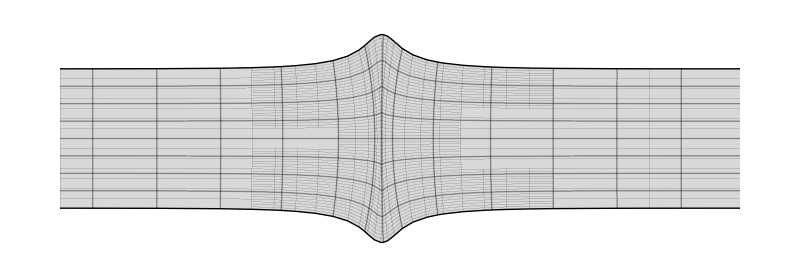

```mathematica
plt=plot[0.005]
```

```mathematica
Export["soliton.pdf",plt]
```

soliton.pdf

```mathematica
table=Monitor[Table[plot[t],{t,0.002,0.01,0.00005}],t];
SetDirectory@NotebookDirectory[];
Export["wave_refined.gif",table]
```

wave_refined.gif

## Soliton in circular rod

```mathematica
Λ
```

12.798

```mathematica
l=-18.9;m=-13.3;n=-10;
ν=0.34;Em=3.7;ρ=1.06;
A=-0.03;
R=5;
c=Sqrt[Em/ρ];v=Sqrt[(A β)/(3ρ)+c^2/(1-ν^2)];
λ = (Em ν)/((1+ν) (1-2ν));μ = Em/(2(1+ν));

β=3Em+2l(1-2ν)^3+4m(1+ν)^2(1-2ν)+6n ν^2;
α1=(1+ν)/4;α2=-(1+ν+2 ν^2)/2;α3=(1+ν)/4;

Λ=Sqrt[(-4((A β+3Em)^2 α1+3Em(A β+3Em)α2+9 Em^2 α3)R^2)/(3A β Em)];
U0[x_,t_]=A Integrate[Cosh[(x-v t)/Λ]^-2,x];
V1[x_,t_]=-ν D[U0[x,t], x](*+(μ(λ+2μ)(4λ+3μ)∂_(x,x,x) U0[x,t]-ρ(3 λ^2+7λ μ+3 μ^2)∂_(x,t,t) U0[x,t])/(16(λ+μ)^2(λ+2μ))-1/(8(λ+μ))(-(2(λ+4l-2m+n)λ)/(λ+μ)-(λ(3λ+3μ+4l-2m))/(λ+μ)^3+4l+2λ)∂_x U0[x,t]^2*);
U2[x_,t_]=(ρ Derivative[0,2][U0][x,t]-2 (λ+μ) Derivative[1,0][V1][x,t]-(λ+2 μ) Derivative[2,0][U0][x,t])/(4 μ)(*+1/(8 μ^2)(2 U0^(1,0)[x,t] ((m+λ+2 μ) ρ U0^(0,2)[x,t]+2 (m λ-2 l μ+(λ+μ)^2) V1^(1,0)[x,t]+(λ (m+λ)+(-2 (l+m)+λ) μ-2 μ^2) U0^(2,0)[x,t])+V1[x,t] ((-4 m+n-4 (λ+μ)) ρ U0^(0,2)[x,t]+2 (-8 l μ+4 m (λ+μ)+2 (λ+μ) (2 λ+μ)-n (λ+2 μ)) V1^(1,0)[x,t]+(λ (4 m-n+4 λ)-2 (4 l-4 m+n-4 λ) μ+8 μ^2) U0^(2,0)[x,t]))*);
V3[x_,t_]=(ρ Derivative[0,2][V1][x,t]-2 (λ+μ) Derivative[1,0][U2][x,t]-μ Derivative[2,0][V1][x,t])/(8 (λ+2 μ))(*-1/(8 (λ+2 μ))((4 m+n+4 (λ+3 μ)) U2[x,t]^2+8 l V1[x,t] U2^(1,0)[x,t]+n V1[x,t] U2^(1,0)[x,t]+2 λ V1[x,t] U2^(1,0)[x,t]+2 μ V1[x,t] U2^(1,0)[x,t]+4 l U0^(1,0)[x,t] U2^(1,0)[x,t]+2 m U0^(1,0)[x,t] U2^(1,0)[x,t]+2 λ U0^(1,0)[x,t] U2^(1,0)[x,t]+2 μ U0^(1,0)[x,t] U2^(1,0)[x,t]+3 m (V1^(1,0)[x,t])^2-1/4 n (V1^(1,0)[x,t])^2+3 λ (V1^(1,0)[x,t])^2+5 μ (V1^(1,0)[x,t])^2+m V1^(1,0)[x,t] U0^(2,0)[x,t]+λ V1^(1,0)[x,t] U0^(2,0)[x,t]+2 μ V1^(1,0)[x,t] U0^(2,0)[x,t]+2 (m+μ) U2[x,t] (4 V1^(1,0)[x,t]+U0^(2,0)[x,t])+2 m V1[x,t] V1^(2,0)[x,t]-1/2 n V1[x,t] V1^(2,0)[x,t]+2 λ V1[x,t] V1^(2,0)[x,t]+2 μ V1[x,t] V1^(2,0)[x,t]+m U0^(1,0)[x,t] V1^(2,0)[x,t]+λ U0^(1,0)[x,t] V1^(2,0)[x,t]+2 μ U0^(1,0)[x,t] V1^(2,0)[x,t]-(2 (2 (l+m+λ)+3 μ) V1[x,t] (- ρ V1^(0,2)[x,t]+2 (λ+μ) U2^(1,0)[x,t]+μ V1^(2,0)[x,t]))/(λ+2 μ)-((2 l+λ) U0^(1,0)[x,t] (-ρ V1^(0,2)[x,t]+2 (λ+μ) U2^(1,0)[x,t]+μ V1^(2,0)[x,t]))/(λ+2 μ))*);
U4[x_,t_]=(ρ Derivative[0,2][U2][x,t]-4 (λ+μ) Derivative[1,0][V3][x,t]-(λ+2 μ) Derivative[2,0][U2][x,t])/(16 μ);
U[x_,r_,t_]=U0[x,t]+U2[x,t] r^2(*+U4[x,t] r^4*);
V[x_,r_,t_]=V1[x,t]r+V3[x,t] r^3;
```

```mathematica
pad=100;
xSc=30;rSc=60;sc=1;
L=500;
xMesh=200;
opts=Sequence[BoundaryStyle->Black,Frame->True,Axes->False,FrameLabel->{{"r, мм",None},{"x, мм",None}},PlotRange->{{0.2L,0.3L},{-2R*sc,2R*sc}},PerformanceGoal->"Quality"];
plot[t_,str_]:=Show[ParametricPlot[{x+xSc U[x,r,t],r+rSc V[x,r,t]},{x,0,L+pad},{r,-R*sc,R*sc},Mesh->{xMesh,7},PlotStyle->Gray,ImageSize->300,Epilog->{Text[Style[ToExpression[str,TeXForm,HoldForm]],Scaled[{0.9,0.92}]]},Evaluate@opts]];
(*Manipulate[plot[t],{t,40,100,1}]*)
```

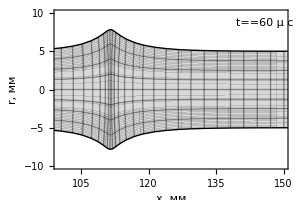

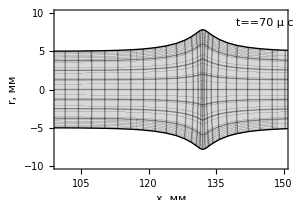

```mathematica
fig1=plot[60,"$t = 60 \\mu c$"]
fig2=plot[70,"$t = 70 \\mu c$"]
(*plot[100,"$t = 100 \\mu s$"]*)
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["DeformedRod1.pdf",fig1]
Export["DeformedRod2.pdf",fig2]
```

DeformedRod1.pdf

DeformedRod2.pdf

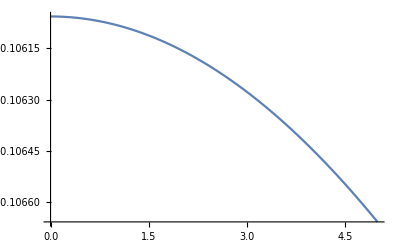

```mathematica
Plot[U[190,r,100],{r,0,R}]
```